```mathematica
Do[
mixlist={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
celldata=Import[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[-1]]<>".csv"}]];
celltype1=Select[celldata,#[[6]]==0&];
celltype2=Select[celldata,#[[6]]==1&];
Pos1=Take[celltype1,All,{2,3}];
Pos2=Take[celltype2,All,{2,3}];
distres=5;
mixinglist={};
Do[
pos1=Pos1[[k]];
pos1list=Select[Pos1,EuclideanDistance[pos1,#]<=distres&];
pos2list=Select[Pos2,EuclideanDistance[pos1,#]<=distres&];
mixing=(Length@pos2list)/(Length@pos1list);
mixinglist=N@Join[mixinglist,{mixing}];
,{k,1,Length@Pos1}];
mixingindex=Mean@mixinglist;
mixlist=Join[mixlist,{mixingindex}];
If[Divisible[j,25]==True,Print["Para No."<>ToString@i<>" mot No."<>ToString@j<>" finished!"]];
,{j,1,50}];
Export[FileNameJoin[{NotebookDirectory[],"data","mixing"<>ToString@i<>".csv"}],mixlist];
,{i,1,10}];
```

```mathematica
paraset2=Import[FileNameJoin[{NotebookDirectory[],"paraset2.csv"}]];
```

```mathematica
GiniCoefficient[data_List]:=Module[{n=Length[data],mean,diffSum},mean=Mean[data];
diffSum=Total[Flatten[Abs[#1-#2]&@@@Tuples[data,2]]];
diffSum/(2 n^2 mean)];
Do[
Sglist={};
grlist={};

model=10^(Log10[80]+(Log10[1600]-Log10[80])*Exp[-Exp[x0*(t-dx)]]);

Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"motile","Para"<>ToString@i,"mot"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
cellcount={};
Do[
celldata=Import[FileNameJoin[{NotebookDirectory[],"motile","Para"<>ToString@i,"mot"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];
cellnum=Length@celldata;
cellcount=Join[cellcount,{cellnum}];
,{k,1,Length@time}];
Sg=60*Flatten@Take[celldata,All,{-1}];
Sgmean=Mean@Sg;
Gini=GiniCoefficient[Sg];
Sglist=Join[Sglist,{{Sgmean,Gini}}];


fit=NonlinearModelFit[fitcount,model,{x0,dx},t];
fasttp=dx/.fit["BestFitParameters"];
Mumax=fit'[fasttp];
grlist=Join[grlist,{Mumax}];
If[Divisible[j,25]==True,Print["Para No."<>ToString@i<>" mot No."<>ToString@j<>" finished!"]]
,{j,1,50}];
Export[FileNameJoin[{NotebookDirectory[],"data","Popgro-"<>ToString@i<>".csv"}],grlist];
Export[FileNameJoin[{NotebookDirectory[],"data","Cellgro-"<>ToString@i<>".csv"}],Sglist];
,{i,20,20}];
```

$Aborted

```mathematica
popdata=Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],"data","Popgro-"<>ToString@i<>".csv"}]],{i,1,20}];
Show[ListPlot[popdata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{-0.2,2.5}},
PlotStyle->Directive[PointSize[0.01],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}],
ListLinePlot[popdata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{0,2.5}},
PlotStyle->Directive[Thickness[0.0025],ColorData[95],Dashing[0.0075]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]];
```

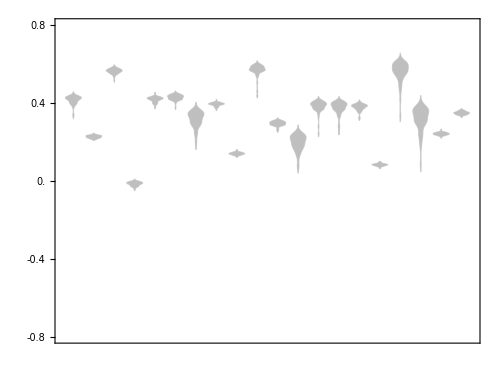

```mathematica
popbase=Flatten[Import[FileNameJoin[{NotebookDirectory[],"data","Popgro-base.csv"}]]];
popbase1=Transpose[Table[popbase,50]][[1;;20]];
popdata1=Log10[popdata/popbase1];
motiledis=DistributionChart[popdata1,ImageSize->500,AspectRatio->0.75,PlotRange->{{0.5,20.5},{-0.8,0.8}},
ChartStyle->GrayLevel[0.75],Frame->True,FrameStyle->Directive[Thickness[0.004],Black,24],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[-0.8,0.8,0.4],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]
```

```mathematica
celldata=Table[Flatten@Transpose[Import[FileNameJoin[{NotebookDirectory[],"data","Cellgro-"<>ToString@i<>".csv"}]]][[1]],{i,1,20}];
Show[ListPlot[celldata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{-0.2,1.6}},
PlotStyle->Directive[PointSize[0.01],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}],
ListLinePlot[celldata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{-0.2,1.6}},
PlotStyle->Directive[Thickness[0.0025],ColorData[95],Dashing[0.0075]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]];
```

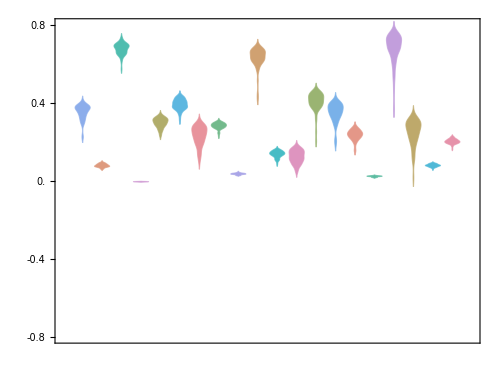

```mathematica
cellbase=Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"data","Cellgro-base.csv"}]],All,{1}];
cellbase1=Transpose[Table[cellbase,50]][[1;;20]];
celldata1=Log10[celldata/cellbase1];
DistributionChart[celldata1,ImageSize->500,AspectRatio->0.75,PlotRange->{{0,21},{-0.8,0.8}},
ChartStyle->ColorData[95],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[-0.8,0.8,0.4],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]
```